```mathematica
ClearAll["Global`*"]
AppendTo[$Path,NotebookDirectory[]]
```

{/home/frank/.Mathematica/DocumentationIndices,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Links,/home/frank/.Mathematica/Kernel,/home/frank/.Mathematica/Autoload,/home/frank/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/home/frank,/usr/local/Wolfram/Mathematica/12.0/AddOns/Packages,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Autoload,/usr/local/Wolfram/Mathematica/12.0/AddOns/Autoload,/usr/local/Wolfram/Mathematica/12.0/AddOns/Applications,/usr/local/Wolfram/Mathematica/12.0/AddOns/ExtraPackages,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Kernel/Packages,/usr/local/Wolfram/Mathematica/12.0/Documentation/English/System,/usr/local/Wolfram/Mathematica/12.0/SystemFiles/Data/ICC,/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv/,/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv/,/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv/,/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv/}

```mathematica
sn = Import["cusp_sn2.csv"];
tr1 = Import["cusp_tr1.csv"];
tr2= Import["cusp_tr2.csv"];
```

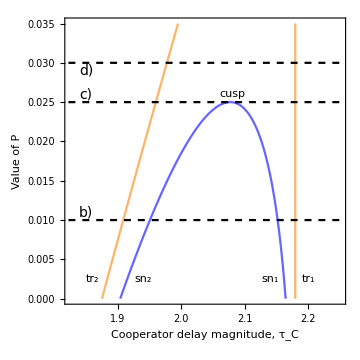

```mathematica
snPlt = ListLinePlot[Transpose[{sn[[;;,1]] ,sn[[;;,2]]}],
PlotRange->{{1.8,2.2}, {0., 0.035}},
PlotStyle->Lighter[Blue,0.4]];
tr1Plt = ListLinePlot[Transpose[{tr1[[;;,1]] ,tr1[[;;,2]]}],
PlotRange->{{1.8,2.2}, {0., 0.035}},
PlotStyle->Lighter[Orange,0.4]];
tr2Plt = ListLinePlot[Transpose[{tr2[[;;,1]] ,tr2[[;;,2]]}],PlotRange->{{1.8,2.2}, {0., 0.035}},
PlotStyle->Lighter[Orange,0.4]];
ScanBeforeCusp=Plot[0.03,{x,1,2.5},PlotStyle->{Black,Dashed}];
ScanAtCusp =Plot[0.025,{x,1,2.5},PlotStyle->{Black,Dashed}];
ScanAfterCusp=Plot[0.01,{x,1,2.5},PlotStyle->{Black,Dashed}];
tr1L = Graphics[{Text[Style[HoldForm[Subscript[tr,1]], Medium,Black], {2.2, 0.0025} ]}, Background->White];
tr2L = Graphics[{Text[Style[HoldForm[Subscript[tr,2]], Medium,Black], {1.86, 0.0025} ]}, Background->White];
sn1L = Graphics[{Text[Style[HoldForm[Subscript[sn,1]], Medium,Black], {2.14, 0.0025} ]}, Background->White];
sn2L = Graphics[{Text[Style[HoldForm[Subscript[sn,2]], Medium,Black], {1.94, 0.0025} ]}, Background->White];
cuspL = Graphics[{Text[Style["cusp", Medium,Black], {2.08, 0.026} ]}, Background->White];

bL = Graphics[{Text[Style["b)",  FontSize->14,Black], {1.85, 0.011} ]}, Background->White];
cL = Graphics[{Text[Style["c)",  FontSize->14,Black], {1.85, 0.026} ]}, Background->White];
dL = Graphics[{Text[Style["d)",  FontSize->14,Black], {1.85, 0.029} ]}, Background->White];
aL = Graphics[{Text[Style["a)",  FontSize->14,Black], ImageScaled[{.18,.93}] ]}, Background->White];

twoParBif = Show[{snPlt,tr1Plt ,tr2Plt,ScanBeforeCusp,ScanAtCusp,ScanAfterCusp,tr1L,tr2L,sn1L,sn2L,cuspL, bL, cL,dL },
PlotRange->{{1.825,2.25}, {0., 0.035}},Frame->True, LabelStyle->{Medium, Black},
FrameLabel->{"Cooperator delay magnitude, τ_C", "Value of P"},ImageSize->Medium,
AspectRatio->1,
PlotRangePadding->None]
```

```mathematica
br = Import["beforeCuspLow_br_eig_lam.csv"];
br1 = Import["beforeCuspLow_br1_eig_lam.csv"];
brU = Import["beforeCuspUp_br_eig_lam.csv"];
br1U = Import["beforeCuspUp_br1_eig_lam.csv"];
```

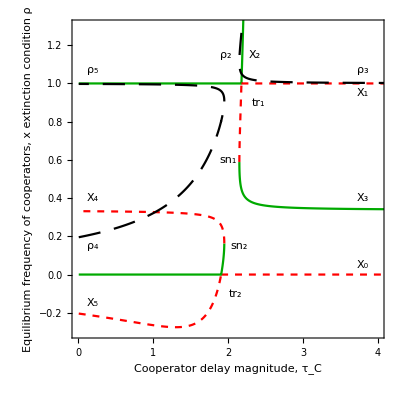

```mathematica
br1Eig=br1[[;;,5]];
br1IdS = Flatten[Position[br1Eig,_?(#<0&)]];
br1tauS = br1[[br1IdS ,1]];
br1XS = br1[[br1IdS ,2]];
br1IdR = Flatten[Position[br1Eig,_?(#>0&)]];
br1tauR = br1[[br1IdR ,1]];
br1XR = br1[[br1IdR ,2]];

br1XRbot =br1XR[[Flatten[Position[br1XR ,_?(#<0&)]]]];
br1tauRbot =br1tauR [[Flatten[Position[br1XR ,_?(#<0&)]]]];

br1XRmid =br1XR[[Flatten[Position[br1XR ,_?(#>0.162911&)]]]];
br1tauRmid =br1tauR [[Flatten[Position[br1XR ,_?(#>0.162911&)]]]];

br1EqS = ListLinePlot[Transpose[{br1tauS ,br1XS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 5.0}, {-0.3, 1.1}}];
br1EqRbot = ListLinePlot[Transpose[{br1tauRbot ,br1XRbot}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 5.0}, {-0.3, 1.1}}];
br1EqRmid = ListLinePlot[Transpose[{br1tauRmid ,br1XRmid}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 5.0}, {-0.3, 1.1}}];

brEig=br[[;;,5]];
brIdS = Flatten[Position[brEig,_?(#<0&)]];
brtauS = br[[brIdS ,1]];
brXS = br[[brIdS ,2]];
brIdR = Flatten[Position[brEig,_?(#>0&)]];
brtauR = br[[brIdR ,1]];
brXR = br[[brIdR ,2]];
brEqS = ListLinePlot[Transpose[{brtauS ,brXS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];
brEqR = ListLinePlot[Transpose[{brtauR ,brXR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];


br1UEig=br1U[[;;,5]];

br1UIdS = Flatten[Position[br1UEig,_?(#<0&)]];
br1UtauS = br1U[[br1UIdS ,1]];
br1UXS = br1U[[br1UIdS ,2]];
br1UIdR = Flatten[Position[br1UEig,_?(#>0&)]];
br1UtauR = br1U[[br1UIdR ,1]];
br1UXR = br1U[[br1UIdR ,2]];

br1UXStop =br1UXS[[Flatten[Position[br1UXS ,_?(#>1&)]]]];
br1UtauStop =br1UtauS[[Flatten[Position[br1UXS ,_?(#>1&)]]]];
br1UEqSTop = ListLinePlot[Transpose[{br1UtauStop,br1UXStop }],PlotStyle->Darker[Green],PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];

br1UEqRTop = ListLinePlot[Transpose[{br1UtauR,br1UXR }],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];






br1UXSMid =br1UXS[[Flatten[Position[br1UXS ,_?(#<0.5886499649835081&)]]]];
br1UtauSMid =br1UtauS[[Flatten[Position[br1UXS ,_?(#<0.5886499649835081&)]]]];
br1UEqSMid = ListLinePlot[Transpose[{br1UtauSMid,br1UXSMid }],PlotStyle->Darker[Green],PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];



brUEig=brU[[;;,5]];
brUIdS = Flatten[Position[brUEig,_?(#<0&)]];
brUtauS = brU[[brUIdS ,1]];
brUXS = brU[[brUIdS ,2]];
brUIdR = Flatten[Position[brUEig,_?(#>0&)]];
brUtauR = brU[[brUIdR ,1]];
brUXR = brU[[brUIdR ,2]];
brUEqS = ListLinePlot[Transpose[{brUtauS ,brUXS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];
brUEqR = ListLinePlot[Transpose[{brUtauR ,brUXR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];


tr1L = Graphics[{Text[Style[HoldForm[Subscript[tr,1]], Medium,Black], {2.4, 0.9} ]}, Background->White];
tr2L = Graphics[{Text[Style[HoldForm[Subscript[tr,2]], Medium,Black], {2.1, -0.1} ]}, Background->White];
sn1L = Graphics[{Text[Style[HoldForm[Subscript[sn,1]], Medium,Black], {2.0, 0.6} ]}, Background->White];
sn2L = Graphics[{Text[Style[HoldForm[Subscript[sn,2]], Medium,Black], {2.15, 0.15} ]}, Background->White];



lamBr1Low = ListLinePlot[Transpose[{br1[[;;,1]] ,br1[[;;,8]]}],PlotRange->{{0.0, 5.0}, {0.0, 1.5}},PlotStyle->{Black,Dashing[{0.04,0.025}]}];
lamBrUp = ListLinePlot[Transpose[{br1U[[;;,1]] ,br1U[[;;,8]]}],PlotRange->{{0.0, 5.0}, {0.0, 1.5}},PlotStyle->{Black,Dashing[{0.04,0.025}]}];
lam2L = Graphics[{Text[Style[HoldForm[Subscript[ρ,2]], Medium,Black], {1.97, 1.15}]}, Background->White];
lam3L = Graphics[{Text[Style[HoldForm[Subscript[ρ,3]], Medium,Black], {3.8, 1.07} ]}, Background->White];

lam4L = Graphics[{Text[Style[HoldForm[Subscript[ρ,4]], Medium,Black], {0.2, 0.15} ]}, Background->White];
lam5L = Graphics[{Text[Style[HoldForm[Subscript[ρ,5]], Medium,Black], {0.2, 1.07} ]}, Background->White];

X0L = Graphics[{Text[Style[HoldForm[Subscript[X,0]], Medium,Black], {3.8, 0.05} ]}, Background->White];
X1L = Graphics[{Text[Style[HoldForm[Subscript[X,1]], Medium,Black], {3.8, 0.95} ]}, Background->White];
X2L = Graphics[{Text[Style[HoldForm[Subscript[X,2]], Medium,Black], {2.35, 1.15} ]}, Background->White];
X3L = Graphics[{Text[Style[HoldForm[Subscript[X,3]], Medium,Black], {3.8, 0.4} ]}, Background->White];
X4L = Graphics[{Text[Style[HoldForm[Subscript[X,4]], Medium,Black], {0.2, 0.4} ]}, Background->White];
X5L = Graphics[{Text[Style[HoldForm[Subscript[X,5]], Medium,Black], {0.2, -0.15} ]}, Background->White];
bL = Graphics[{Text[Style["b)",  FontSize->14,Black], ImageScaled[{.18,.93}] ]}, Background->White];
beforeCusp=Show[{brEqS,brEqR ,br1EqS ,br1EqRbot,br1EqRmid,br1UEqSTop,brUEqS ,brUEqR ,br1UEqRTop ,br1UEqSMid,tr1L,tr2L ,sn1L,sn2L,lamBr1Low,X0L,X1L,X2L,X3L ,X4L,X5L ,lamBrUp,lam3L ,lam2L,lam4L,lam5L},PlotRange->{{0.0, 4.0}, {-0.3, 1.3}},Frame->True,
FrameLabel->{"Cooperator delay magnitude, τ_C",  "Equilibrium frequency\n of cooperators, x \n extinction condition ρ"},
Axes->False,LabelStyle->Directive[Black,14],
AspectRatio->1,
PlotRangePadding->None]
```

```mathematica
br = Import["afterCuspLow_br_eig_lam.csv"];
br1 = Import["afterCuspLow_br1_eig_lam.csv"];
brU = Import["afterCuspUp_br_eig_lam.csv"];
br1U = Import["afterCuspUp_br1_eig_lam.csv"];
```

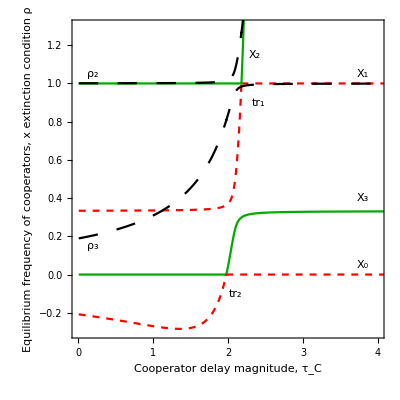

```mathematica
brEig=br[[;;,5]];
brIdS = Flatten[Position[brEig,_?(#<0&)]];
brtauS = br[[brIdS ,1]];
brXS = br[[brIdS ,2]];
brIdR = Flatten[Position[brEig,_?(#>0&)]];
brtauR = br[[brIdR ,1]];
brXR = br[[brIdR ,2]];
brEqS = ListLinePlot[Transpose[{brtauS ,brXS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];
brEqR = ListLinePlot[Transpose[{brtauR ,brXR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];


brUEig=brU[[;;,5]];
brUIdS = Flatten[Position[brUEig,_?(#<0&)]];
brUtauS = brU[[brUIdS ,1]];
brUXS = brU[[brUIdS ,2]];
brUIdR = Flatten[Position[brUEig,_?(#>0&)]];
brUtauR = brU[[brUIdR ,1]];
brUXR = brU[[brUIdR ,2]];
brUEqS = ListLinePlot[Transpose[{brUtauS ,brUXS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];
brUEqR = ListLinePlot[Transpose[{brUtauR ,brUXR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];




br1Eig=br1[[;;,5]];
br1IdS = Flatten[Position[br1Eig,_?(#<0&)]];
br1tauS = br1[[br1IdS ,1]];
br1XS = br1[[br1IdS ,2]];
br1IdR = Flatten[Position[br1Eig,_?(#>0&)]];
br1tauR = br1[[br1IdR ,1]];
br1XR = br1[[br1IdR ,2]];
br1EqS = ListLinePlot[Transpose[{br1tauS ,br1XS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 4.0}, {-0.3, 1.1}}];
br1EqR = ListLinePlot[Transpose[{br1tauR ,br1XR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 4.0}, {-0.3, 1.1}}];


br1UEig=br1U[[;;,5]];
br1UIdS = Flatten[Position[br1UEig,_?(#<0&)]];
br1UtauS = br1U[[br1UIdS ,1]];
br1UXS = br1U[[br1UIdS ,2]];
br1UIdR = Flatten[Position[br1UEig,_?(#>0&)]];
br1UtauR = br1U[[br1UIdR ,1]];
br1UXR = br1U[[br1UIdR ,2]];
br1UEqS = ListLinePlot[Transpose[{br1UtauS ,br1UXS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];
br1UEqR = ListLinePlot[Transpose[{br1UtauR ,br1UXR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];

br1[[;;,8]];
lamBr1Low = ListLinePlot[Transpose[{br1[[;;,1]] ,br1[[;;,8]]}],PlotRange->{{0.0, 5.0}, {0.0, 1.1}},PlotStyle->{Black, Dashing[Large]}];
lamBrUp = ListLinePlot[Transpose[{br1U[[;;,1]] ,br1U[[;;,8]]}],PlotRange->{{0.0, 5.0}, {0.0, 1.5}},PlotStyle->{Black, Dashing[Large]}];

tr1L = Graphics[{Text[Style[HoldForm[Subscript[tr,1]], Medium,Black], {2.4, 0.9} ]}, Background->White];
tr2L = Graphics[{Text[Style[HoldForm[Subscript[tr,2]], Medium,Black], {2.1, -0.1} ]}, Background->White];
X0L = Graphics[{Text[Style[HoldForm[Subscript[X,0]], Medium,Black], {3.8, 0.05} ]}, Background->White];
X1L = Graphics[{Text[Style[HoldForm[Subscript[X,1]], Medium,Black], {3.8, 1.05} ]}, Background->White];
X2L = Graphics[{Text[Style[HoldForm[Subscript[X,2]], Medium,Black], {2.35, 1.15} ]}, Background->White];
X3L = Graphics[{Text[Style[HoldForm[Subscript[X,3]], Medium,Black], {3.8, 0.4} ]}, Background->White];
X4L = Graphics[{Text[Style[HoldForm[Subscript[X,4]], Medium,Black], {0.2, 0.4} ]}, Background->White];
X5L = Graphics[{Text[Style[HoldForm[Subscript[X,5]], Medium,Black], {0.2, -0.15} ]}, Background->White];
lam3L = Graphics[{Text[Style[HoldForm[Subscript[ρ,3]], Medium,Black], {0.2, 0.15} ]}, Background->White];
lam2L = Graphics[{Text[Style[HoldForm[Subscript[ρ,2]], Medium,Black], {0.2, 1.05} ]}, Background->White];
dL = Graphics[{Text[Style["d)",  FontSize->14,Black], ImageScaled[{.18,.93}] ]}, Background->White];

afterCusp =Show[{brEqS,brEqR ,brUEqS ,brUEqR ,br1EqS,br1EqR,br1UEqS,br1UEqR,lamBr1Low ,lamBrUp ,tr1L,tr2L,X0L,X1L,X2L,X3L  ,lam3L ,lam2L},PlotRange->{{0.0, 4.0}, {-0.3, 1.3}},Frame->True,
FrameLabel->{"Cooperator delay magnitude, τ_C",  "Equilibrium frequency\n of cooperators, x \n extinction condition ρ"},
Axes->False,LabelStyle->Directive[Black,14],
AspectRatio->1,
PlotRangePadding->None]
```

```mathematica
br = Import["atCuspUp_br_eig_lam.csv"];
br1 = Import["atCuspUp_br1_eig_lam.csv"];
br2 = Import["atCuspUp_br2_eig_lam.csv"];
br3 = Import["atCuspUp_br3_eig_lam.csv"];
```

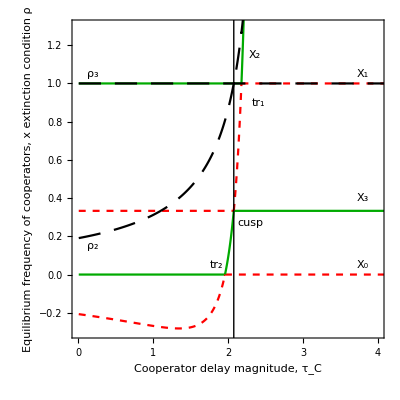

```mathematica
brEig=br[[;;,5]];
brIdS = Flatten[Position[brEig,_?(#<0&)]];
brtauS = br[[brIdS ,1]];
brXS = br[[brIdS ,2]];
brIdR = Flatten[Position[brEig,_?(#>0&)]];
brtauR = br[[brIdR ,1]];
brXR = br[[brIdR ,2]];
brEqS = ListLinePlot[Transpose[{brtauS ,brXS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];
brEqR = ListLinePlot[Transpose[{brtauR ,brXR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];

br3Eig=br3[[;;,5]];
br3IdS = Flatten[Position[br3Eig,_?(#<0&)]];
br3tauS = br3[[br3IdS ,1]];
br3XS = br3[[br3IdS ,2]];
br3IdR = Flatten[Position[br3Eig,_?(#>0&)]];
br3tauR = br3[[br3IdR ,1]];
br3XR = br3[[br3IdR ,2]];
br3EqS = ListLinePlot[Transpose[{br3tauS ,br3XS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];
br3EqR = ListLinePlot[Transpose[{br3tauR ,br3XR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];

br2Eig=br2[[;;,5]];
br2IdS = Flatten[Position[br2Eig,_?(#<0&)]];
br2tauS = br2[[br2IdS ,1]];
br2XS = br2[[br2IdS ,2]];
br2IdR = Flatten[Position[br2Eig,_?(#>0&)]];
br2tauR = br2[[br2IdR ,1]];
br2XR = br2[[br2IdR ,2]];
br2EqS = ListLinePlot[Transpose[{br2tauS ,br2XS}],PlotStyle->Darker[Green],PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];
br2EqR = ListLinePlot[Transpose[{br2tauR ,br2XR}],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 4.0}, {-0.2, 1.1}}];


br1Eig=br1[[;;,5]];
ListLinePlot[Transpose[{br1[[;;,1]]  ,br1[[;;,2]] }],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];


br1IdS = Flatten[Position[br1Eig,_?(#<0&)]];
br1tauS = br1[[br1IdS ,1]];
br1XS = br1[[br1IdS ,2]];
br1IdR = Flatten[Position[br1Eig,_?(#>0&)]];
br1tauR = br1[[br1IdR ,1]];
br1XR = br1[[br1IdR ,2]];

br1XRbot =br1XR[[Flatten[Position[br1XR ,_?(#<0&)]]]];
br1tauRbot =br1tauR [[Flatten[Position[br1XR ,_?(#<0&)]]]];
br1EqBot = ListLinePlot[Transpose[{br1tauRbot  ,br1XRbot  }],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];

br1XSmid =br1XS[[Flatten[Position[br1XS ,_?(#<1&)]]]];
br1tauSmid =br1tauS [[Flatten[Position[br1XS ,_?(#<1&)]]]];
br1SEqmid = ListLinePlot[Transpose[{br1tauSmid ,br1XSmid }],PlotStyle->Darker[Green],PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];

br1XSTop =br1XS[[Flatten[Position[br1XS ,_?(#>1&)]]]];
br1tauSTop=br1tauS [[Flatten[Position[br1XS ,_?(#>1&)]]]];
br1SEqTop = ListLinePlot[Transpose[{br1tauSTop,br1XSTop }],PlotStyle->Darker[Green],PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];


br1XRmid=br1XR[[Flatten[Position[br1XR ,_?(#>0&)]]]];
br1tauRmid =br1tauR [[Flatten[Position[br1XR ,_?(#>0&)]]]];
br1REqmid = ListLinePlot[Transpose[{br1tauRmid  ,br1XRmid  }],PlotStyle->{Red, Dashed},PlotRange->{{0.0, 5.0}, {-0.3, 1.9}}];

tr1L = Graphics[{Text[Style[HoldForm[Subscript[tr,1]], Medium,Black], {2.4, 0.9} ]}, Background->White];
tr2L = Graphics[{Text[Style[HoldForm[Subscript[tr,2]], Medium,Black], {1.85, 0.05} ]}, Background->White];
cuspL = Graphics[{Text[Style["cusp", Medium,Black], {2.3, 0.27} ]}, Background->White];


X0L = Graphics[{Text[Style[HoldForm[Subscript[X,0]], Medium,Black], {3.8, 0.05} ]}, Background->White];
X1L = Graphics[{Text[Style[HoldForm[Subscript[X,1]], Medium,Black], {3.8, 1.05} ]}, Background->White];
X2L = Graphics[{Text[Style[HoldForm[Subscript[X,2]], Medium,Black], {2.35, 1.15} ]}, Background->White];
X3L = Graphics[{Text[Style[HoldForm[Subscript[X,3]], Medium,Black], {3.8, 0.4} ]}, Background->White];
X4L = Graphics[{Text[Style[HoldForm[Subscript[X,4]], Medium,Black], {0.2, 0.4} ]}, Background->White];
X5L = Graphics[{Text[Style[HoldForm[Subscript[X,5]], Medium,Black], {0.2, -0.15} ]}, Background->White];
cL = Graphics[{Text[Style["c)",  FontSize->14,Black], ImageScaled[{.18,.93}] ]}, Background->White];

lamBr1Low = ListLinePlot[Transpose[{br1[[;;,1]] ,br1[[;;,8]]}],PlotRange->{{0.0, 5.0}, {0.0, 1.5}},PlotStyle->{Black,Dashing[{0.04,0.025}]}];
lamBrUp = ListLinePlot[Transpose[{br2[[;;,1]] ,br2[[;;,8]]}],PlotRange->{{0.0, 5.0}, {0.0, 1.5}},PlotStyle->{Black,Dashing[{0.04,0.025}]}];
lamBrUpTest = ListLinePlot[Transpose[{br2[[;;,1]] ,br2[[;;,2]]}],PlotRange->{{0.0, 5.0}, {0.0, 1.5}},PlotStyle->{Black,Dashing[{0.04,0.025}]}];

lam3L = Graphics[{Text[Style[HoldForm[Subscript[ρ,2]], Medium,Black], {0.2, 0.15} ]}, Background->White];
lam2L = Graphics[{Text[Style[HoldForm[Subscript[ρ,3]], Medium,Black], {0.2, 1.05} ]}, Background->White];

atCusp =Show[{brEqS,brEqR ,br3EqS,br3EqR ,br2EqS,br2EqR ,br1EqBot,br1SEqmid,br1REqmid,br1SEqTop  ,tr1L  ,tr2L,cuspL  ,X0L,X1L,X2L,X3L  ,lamBr1Low ,lamBrUp ,lam3L,lam2L},PlotRange->{{0.0, 4.0}, {-0.3, 1.3}},Frame->True,
FrameLabel->{"Cooperator delay magnitude, τ_C",  "Equilibrium frequency\n of cooperators, x \n extinction condition ρ"},
Axes->False,LabelStyle->Directive[Black,14],
AspectRatio->1,
PlotRangePadding->None,
Epilog->Line[{{2.077080349626964,-0.5},{2.077080349626964,1.5}}],PlotStyle->{Gray}]
```

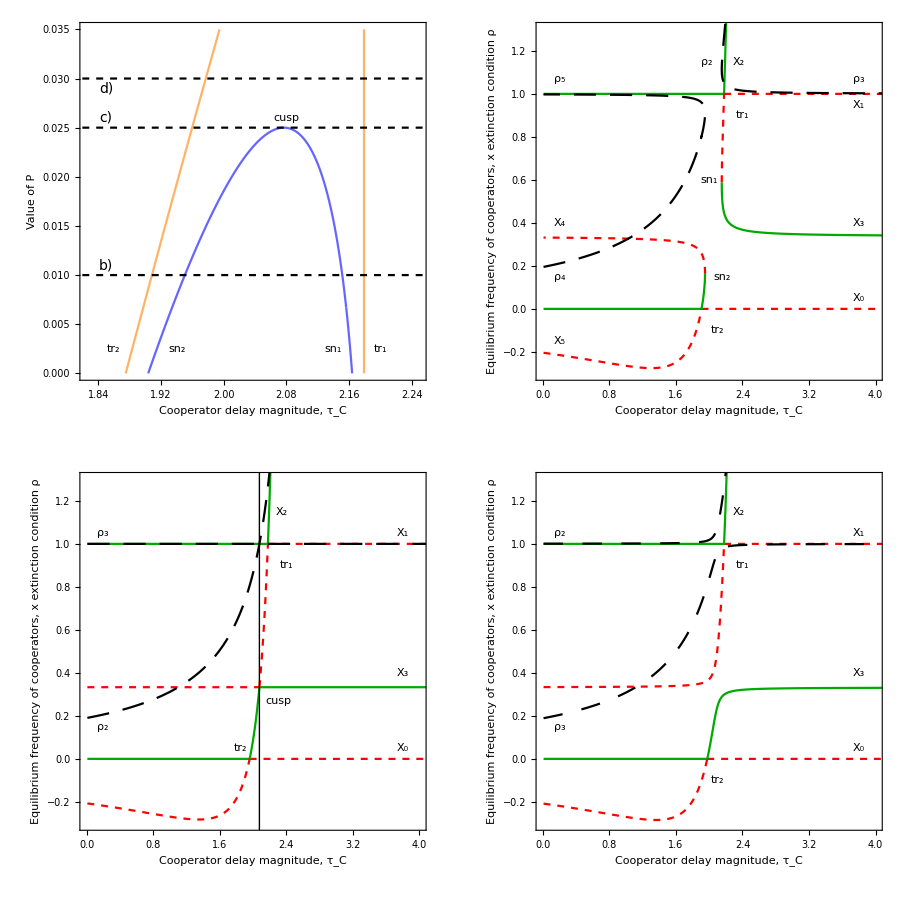

/home/frank/Gosia/Git2/compartmentalised_timedelays/Julia/csv

cusp_subplots.pdf

```mathematica
gridPic = GraphicsGrid[{{twoParBif,beforeCusp },{atCusp  ,afterCusp  }},ImageSize->{900,900},Spacings->{10,0}]
SetDirectory[NotebookDirectory[]]
Export["cusp_subplots.pdf",gridPic,"PDF","AllowRasterization"->False]
```